```mathematica
ClearAll["Global`*"]
μB=9.27*^-24;
μN=5.050784*^-27;
h=6.626*^-34;
ℏ=h/(2π);
kB=1.38*^-23;
μ0=4π*1*^-7;

γY=2.1*^6;
γV=11.2*^6;
gYbgEl=6.08;
gYbNuc=0.98734;
γYbEl=(gYbgEl*μB)/h;
γYbNuc=(gYbNuc*μN)/h;
SYb=1/2;
IYb=1/2;
IY=1/2;
IV=7/2;
tt440={0.4005,0.4796,0.5851,0.6852,0.7801,0.8961,0.991,1.0966,1.1914,1.2968,1.397,1.5024,1.6237,1.6974,1.8082,1.9189,1.9768,2.2403,2.5144,2.7306,3.0099,3.2417,3.5053,3.7582,4.0165,4.2589,4.5224,4.7753,5.0177,5.2495,5.4812,5.7393,6.0029,6.2609,6.5083,6.756,6.998,7.2563,7.4983,7.7614,8.0145,8.5088,8.7516}/1000;
ee440={0.8199,0.7894,0.7931,0.76,0.7457,0.7562,0.7212,0.7279,0.6814,0.6654,0.6258,0.6227,0.5856,0.5481,0.548,0.5276,0.5057,0.4493,0.4049,0.3718,0.3367,0.284,0.2488,0.2201,0.1955,0.1681,0.1438,0.1248,0.1063,0.0893,0.0715,0.0576,0.0516,0.0404,0.0296,0.0262,0.0175,0.0157,0.0101,7.39*^-3,6.63*^-3,2.61*^-3,2.92*^-3};
data440=Transpose[{tt440,ee440}];
dataLogSq440=Transpose[{tt440,Log[ee440^2]}];
tt60={0.2028,0.2084,0.2403,0.2748,0.2883,0.3306,0.3465,0.3576,0.3921,0.4134,0.4612,0.4909,0.5199,0.5438,0.5705,0.5949,0.6158,0.6526,0.6768}/1000;
ee60={0.8998,0.7109,0.5819,0.4686,0.3826,0.3409,0.3059,0.2128,0.1682,0.1502,0.1127,0.0705,0.0662,0.0566,0.0451,0.0287,0.0306,0.032,0.0222};
data60=Transpose[{tt60,ee60}];
dataLogSq60=Transpose[{tt60,Log[ee60^2]}];
tt1360={5.4207,8.2299,10.7057,13.5821,16.1238,18.6663,21.341,23.9505,26.6265,29.2341,31.7077,34.5843,36.9234,39.733,42.4064,44.9472,47.5521,50.0937,52.8314,55.4386,58.1081,60.6472,63.1849,66.0553,68.5901,71.1959,73.9294,76.3306,79.0691,81.5325,84.2659,86.8545,89.667,92.1928,94.7187,97.4477,99.8996,102.6434,105.1717}/10^6;
ee1360={0.9745,0.9245,0.9076,0.8658,0.8262,0.8065,0.7522,0.7342,0.7085,0.6571,0.6095,0.5847,0.5332,0.5116,0.4612,0.4302,0.3727,0.3556,0.2993,0.2761,0.2247,0.2003,0.1724,0.1412,0.113,0.1001,0.0757,0.0609,0.0525,0.0373,0.0282,0.016,0.0166,0.0105,6.65*^-3,4.49*^-3,2.37*^-3,2.34*^-3,1.58*^-3};
data1360=Transpose[{tt1360,ee1360}];
dataLogSq1360=Transpose[{tt1360,Log[ee1360^2]}];
tt510={5.4872,8.1621,10.8385,13.378,15.9864,18.5941,21.2675,23.8107,26.551,29.0249,31.5648,34.4379,36.9111,39.6522,42.1905,44.9969,47.5365,50.0744,52.8129,55.4817,58.2863,60.6247,63.0253,65.8959,68.5644,71.2328,73.7625,76.2245,79.098,81.5476,84.2219,86.8784,89.5287,97.3548,99.8067,105.16,94.6438}/10^6;
ee510={0.9635,0.9037,0.882,0.7952,0.7545,0.7037,0.6343,0.6298,0.5676,0.5295,0.4828,0.423,0.3879,0.3577,0.3135,0.2762,0.249,0.2157,0.1858,0.1487,0.1252,0.1122,0.0888,0.0731,0.0581,0.0462,0.0323,0.0222,0.0196,9.80*^-3,9.04*^-3,5.29*^-3,2.63*^-3,2.30*^-3,1.21*^-3,1.17*^-3,9.64*^-4};
data510=Transpose[{tt510,ee510}];
dataLogSq510=Transpose[{tt510,Log[ee510^2]}];
tt340={5.4881,10.5034,16.0472,21.192,26.538,31.8193,36.8957,42.2406,47.5147,52.7881,58.1883,63.2021,68.3887,73.951,79.0509}/10^6;
ee340={0.9856,0.8723,0.6435,0.5083,0.4061,0.3433,0.2607,0.2024,0.1419,0.0977,0.0562,0.0478,0.0198,0.0235,0.0327};
data340=Transpose[{tt340,ee340}];
dataLogSq340=Transpose[{tt340,Log[ee340^2]}];
neY=(33791/2)/(4/3*π*(Sqrt[56.95^2+56.95^2+50.31^2]*10^-10)^3);(*Num density of Y*)
Print["Number density of Y = " <> ToString[neY, InputForm]]
```

Number density of Y = 4.710192810162301*^27

```mathematica
(*Rates and magnetic field fluctuations. Only take ΔB//z since we assume B//z and all gradients are //z.*)
(*RYb=1000;*)
RV=0.25*μ0*h*γV^2*neY*Sqrt[IV*(IV+1)];
RY=0.25*μ0*h*γY^2*neY*Sqrt[IY*(IY+1)];
ΔBYb=0.66/10^4;
ΔBV=(1.5*2.35)/10^4;
ΔBY=(0.017*2.35)/10^4;
ΔBYFrozen=(0.0017*2.35)/10^4;
ΔBVFrozen=(0.0684*2.35)/10^4;
```

```mathematica
(*Convert magnetic field fluctuations to transition fluctuations based on the accessed transition and the applied field.*)
(*TransSens=1.44287*^7;*)(*For 0.44T along z. Hz/T transition for 1->2 ground*)
(*TransSens=3.7*^8;*)(*For 0.06T along z*)
(*TransSens=25.0*^9;*)(*For 1.36T along z. Hz/T transition for ground 1->1 excited*)
ΓSDYb=ΔBYb*TransSens;
ΓSDV=ΔBV*TransSens;
ΓSDY=ΔBY*TransSens;
ΓSDVFrozen=ΔBVFrozen*TransSens;
ΓSDYFrozen=ΔBYFrozen*TransSens;
```

```mathematica
largeModel=I0-4*t*π*(Γ0+1/2 ΓSDVFrozen*RV*t+1/2 ΓSDYFrozen*RY*t+ΓSDYb*Sech[(gYbgEl*μB*B)/(2*kB*T)]^2*Sqrt[2/(π*RYb*t)]);
smallModelΓ0=I0-4*t*π*(Γ0+1/2 ΓSDVFrozen*RV*t+1/2 ΓSDYFrozen*RY*t+1/2 ΓSDYb*RYb*t*Sech[(gYbgEl*μB*B)/(2*kB*T)]^2);
smallModelΓSDV=I0-4*t*π*(1800+1/2 ΓSDVFrozenIter*RV*t+1/2 ΓSDYFrozen*RY*t+1/2 ΓSDYb*RYb*t*Sech[(gYbgEl*μB*B)/(2*kB*T)]^2)
smallModelAll=I0-4*t*π*(Γ0+ΓSDIter*t);
```

I0-4 π t (1800+7.4799×10^-7 t TransSens+244.054 t ΓSDVFrozenIter+0.000033 RYb t TransSens Sech[(2.04209 B)/T]^2)

R * Mean t12 = 0.0000554257 RYb

{I0→0.881224,ΓSDVFrozenIter→300164.}

{I0→0.489674,ΓSDVFrozenIter→216286.}

{I0→0.0690585,ΓSDVFrozenIter→10000.}

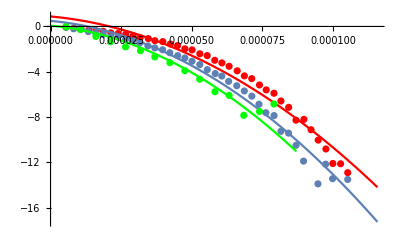

```mathematica
data1=dataLogSq1360;
Print["R * Mean t12 = " <> ToString[RYb*Mean[data1⟦;;,1⟧]]]
model1=smallModelΓSDV/.{B->1.36,T->0.65,RYb->1200,TransSens->25*^9};
sol1=FindFit[data1,{model1},{{I0,0},ΓSDVFrozenIter},t]
(*sol1=FindFit[data1{model1, {Γ0>0}},{{I0,0},Γ0},t]*)

data2=dataLogSq510;
model2=smallModelΓSDV/.{B->0.51,T->0.65,RYb->300,TransSens->25*^9};
sol2=FindFit[data2,{model2},{{I0,0},ΓSDVFrozenIter},t]

data3=dataLogSq340;
model3=smallModelΓSDV/.{B->0.34,T->0.65,RYb->300,TransSens->25*^9};
sol3=FindFit[data3,{model3,{ΓSDVFrozenIter>10000}},{{I0,0},ΓSDVFrozenIter},t]

Show[ListPlot[data1,PlotStyle->Red], 
Plot[model1/.sol1,{t,0,1.1*Max[data1⟦;;,1⟧]},PlotStyle->Red],
ListPlot[data2],
Plot[model2/.sol2,{t,0,1.1*Max[data2⟦;;,1⟧]}],
ListPlot[data3,PlotStyle->Green],
Plot[model3/.sol3,{t,0,1.1*Max[data3⟦;;,1⟧]},PlotStyle->Green],PlotRange->All
]
```

{I0→2.688,ΓSDIter→0.912692,Γ0→1236.04}

{I0→-0.38242,ΓSDIter→10172.1,Γ0→15.6353}

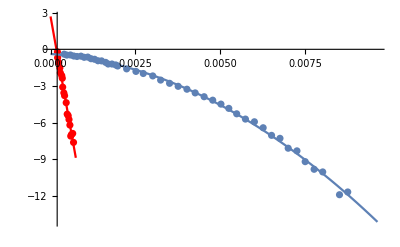

```mathematica
data4=dataLogSq60;
model4=smallModelAll/.{B->0.06,T->0.7,RYb->300,TransSens->3.7*^8};
sol4=FindFit[data4,{model4,{ΓSDIter>0}},{{I0,0},ΓSDIter, Γ0},t]

data5=dataLogSq440;
model5=smallModelAll/.{B->0.44,T->0.7,RYb->300,TransSens->1.44*^7};
sol5=FindFit[data5,{model5,{ΓSDIter>0}},{{I0,0},ΓSDIter, Γ0},t]

Show[
ListPlot[data4,PlotStyle->Red], 
Plot[model4/.sol4,{t,0,1.1*Max[data4⟦;;,1⟧]},PlotStyle->Red],
ListPlot[data5],
Plot[model5/.sol5,{t,0,1.1*Max[data5⟦;;,1⟧]}], PlotRange->All
]
```

{I0→-0.516515,Tm→0.00683448,x→1.8469}

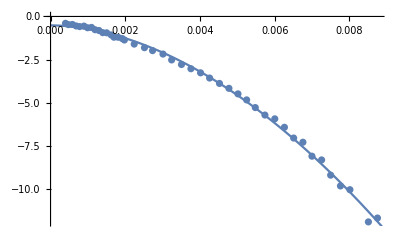

```mathematica
modelMim=I0-2*((2t)/Tm)^x;
solMim=FindFit[data5,{modelMim},{I0,{Tm,0.00006},{x,2}},t]
Show[ListPlot[data5], Plot[modelMim/.solMim,{t,0,1.1*Max[data5⟦;;,1⟧]}]]
```

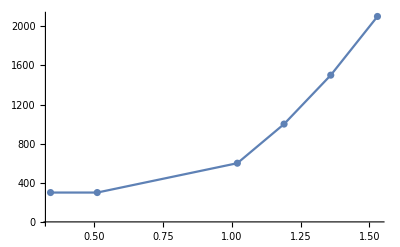

```mathematica
B={1.0,1.5,3.0,3.5,4.0,4.5}*0.34;
RYbArr={300,300,600,1000,1500,2100};
RYbInt=Interpolation[Transpose[{B,RYbArr}]];
Show[ListPlot[Transpose[{B, RYbInt/@B}]],ListLinePlot[Transpose[{B, RYbInt/@B}]]]
```

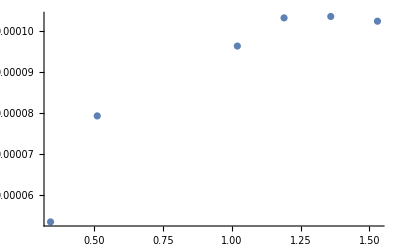

```mathematica
TmArr={0.053333905633941,0.079306097790739,0.096422367414220,0.103325432079306,0.103673871367643,0.102507703281979}*10^-3;
ListPlot[Transpose[{B,TmArr}]]
```

```mathematica
Manipulate[
Show[
b=1/2*BV*25*^9*488+1/2*BYb*25*^9*RYbInt[BB]*Sech[3.14*BB]^2;
Plot[1/b*(-a+Sqrt[a^2+2*b/π]),{BB,0.35,1.53}],
ListPlot[Transpose[{B,TmArr}]],PlotRange->{{0.3,1.6},{0.00004,0.00011}},AxesOrigin->{0.3,0.00004}],
{{BV,6.148*^-6},1*^-6,1*^-4},{{BYb,9.86*^-5},6*^-6,6*^-4},{{a,1160},0,10000}]
```

{a→1244.36,BV→5.73316×10^-6,BYb→0.0000817739}

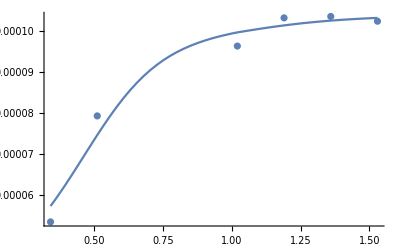

```mathematica
sol1=FindFit[Transpose[{B,TmArr}],{1/(1/2*BV*25*^9*488+1/2*BYb*25*^9*RYbInt[BB]*Sech[3.14*BB]^2)*(-a+Sqrt[a^2+2*(1/2*BV*25*^9*488+1/2*BYb*25*^9*RYbInt[BB]*Sech[3.14*BB]^2)/π]),
{a>0}},{{a,1200},{BV,6*^-6},{BYb,9.86*^-5}},BB]
Show[
ListPlot[Transpose[{B,TmArr}]],
Plot[1/(1/2*BV*25*^9*488+1/2*BYb*25*^9*RYbInt[BB]*Sech[3.14*BB]^2)*(-a+Sqrt[a^2+2*(1/2*BV*25*^9*488+1/2*BYb*25*^9*RYbInt[BB]*Sech[3.14*BB]^2)/π])/.sol1,{BB,0.34,1.53}]
]
```

{a→1044.45}

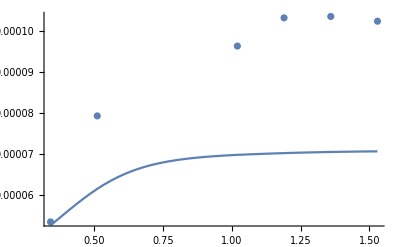

```mathematica
sol1=FindFit[Transpose[{B,TmArr}],{1/(1/2*1.6*^-5*25*^9*488+1/2*6.6*^-5*25*^9*RYbInt[BB]*Sech[3.14*BB]^2)*(-a+Sqrt[a^2+2*(1/2*1.6*^-5*25*^9*488+1/2*6.6*^-5*25*^9*RYbInt[BB]*Sech[3.14*BB]^2)/π]),
{a>0}},{{a,1000}},BB]
Show[
ListPlot[Transpose[{B,TmArr}]],
Plot[1/(1/2*1.6*^-5*25*^9*488+1/2*6.6*^-5*25*^9*RYbInt[BB]*Sech[3.14*BB]^2)*(-a+Sqrt[a^2+2*(1/2*1.6*^-5*25*^9*488+1/2*6.6*^-5*25*^9*RYbInt[BB]*Sech[3.14*BB]^2)/π])/.sol1,{BB,0.34,1.53}]
]
```

```mathematica
Manipulate[
LogLinearPlot[1/b*(-a+Sqrt[a^2+2*b/π]),{b,1*^3,1*^7},PlotRange->{0,0.0004}],
{a,1000,3000}]
```

```mathematica
1/(π*1000)//N
```

0.00031831

```mathematica
ClearAll[b]
```

```mathematica
Solve[-4*t*π*(a+b*t)==-2,t]
```

{{t→(-a π-√π √(2 b+a^2 π))/(2 b π)},{t→(-a π+√π √(2 b+a^2 π))/(2 b π)}}

```mathematica
Solve[-4*t*π*(a+ΓSD*Sqrt[2/(π*R*t)])==-2,t]
```

{{t→(a+(2 ΓSD^2)/R-(2 √(a R ΓSD^2+ΓSD^4))/R)/(2 a^2 π)},{t→(a+(2 ΓSD^2)/R+(2 √(a R ΓSD^2+ΓSD^4))/R)/(2 a^2 π)}}

```mathematica
2*1000*FullSimplify[(a+(2 ΓSD^2)/R-(2 √(a R ΓSD^2+ΓSD^4))/R)/(2 a^2 π)]/.{a->1200,ΓSD->9.86*^-5*0.0143*^9,R->300}
```

0.0110305

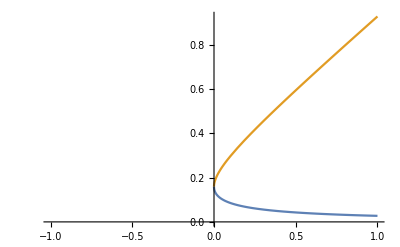

```mathematica
Plot[{(1+2x-2 √(x+x^2))/(2 π),(1+2x+2 √(x+x^2))/(2 π)},{x,-1,1}]
```

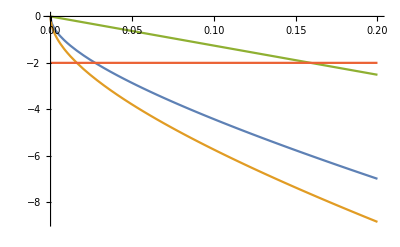

```mathematica
Plot[{-4*t*π*(1+Sqrt[2/(π*t)]),-4*t*π*(1+Sqrt[2*2/(π*t)]),-4*t*π*(1+Sqrt[0*2/(π*t)]),-2},{t,0,0.2}]
```

```mathematica
(1+2x-2 √(x+x^2))/(2 π)/.x->2//N
```

0.0160779

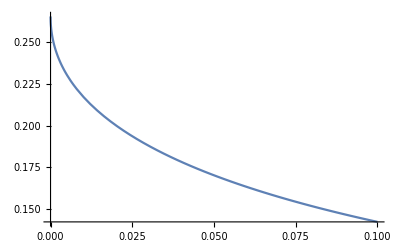

```mathematica
Plot[(1+2x-2 √(x+x^2))/(2 π*1200)*2*1000,{x,0,0.1},PlotRange->All]
```

```mathematica
9.86*^-5*0.0143*^9
```

1409.98

```mathematica
2*300/(9.86*^-5*0.0143*^9*Sech[3.14*0.444]^2)^2*1000
2*300/(9.86*^-5*0.0307*^9*Sech[3.14*0.24]^2)^2*1000
2*300/(9.86*^-5*0.37*^9*Sech[3.14*0.06]^2)^2*1000
300*{0.5,1.5,4.5}/10^3
```

6.32746

0.185675

0.000483775

{0.15,0.45,1.35}